# “Simple mathematical models with very complicated dynamics“

### Warunki początkowe

```mathematica
nmax=500; (* długość ciągu Subscript[x, n]*)
nlambda=500; (* liczba wartości λ*)
x0=0.01; (* punkt początkowy*)
```

### Definicja funkcji dla danego λ

```mathematica
f[λ_]:={
x=Table[0,{n,nmax}]; (* inicjalizacja tablicy w pamięci *)
x[[1]]=x0; (* inicjalizacja warunku początkowego *)
For[n=2,n≤nmax,n++,x[[n]]=λ (1-x[[n-1]]) x[[n-1]]]; (* generacja ciągu rekurencyjnego *)
Table[{λ,x[[n]]},{n,nmax/2,nmax}] (* dane po ustabilizowaniu w formacie (x,y) *)
}
```

### Tworzenie tablicy zawierającej dane do wykresu

```mathematica
A=Table[f[λ=2+2(i-1)/nlambda],{i,1,nlambda}]; (* generowanie danych do wykresu *)
P=Flatten[A,1]; (* spłaszczanie listy wygenerowanych punktów danych *)
```

### Rysowanie diagramu bifurkacji

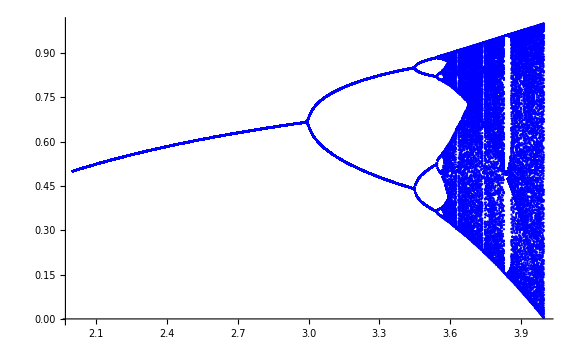

```mathematica
ListPlot[P,ImageSize->Large,PlotStyle->Blue,PlotStyle->PointSize[0.001]] (* jednokolorowy wykres *)
```